Inicialización netlogo

```mathematica
<<NetLogo`
$NLHome= "/opt/netlogo-4.0.5";
$NLModel="/home/erikasv/github/Collective-intelligence--Analysis-and-modeling";
NLStart[];
NLCommand["no-display"];
NLLoadModel[ToFileName[{$NLModel},"modelo.nlogo"]];
```

Definición de experimentos:
People, selection-size

```mathematica
ExpPeopleSize[p_,s_,n_]:=Module[{},
NLCommand["set num-people ",p, "set selection-size ",s,"setup"];
Mean[NLDoReport["go","clustering-coefficient",n]]
];
people=Table[{i,j,2},{i,10,100,10},{j,1,100,20}];
NLCommand["no-display"];
```

```mathematica
clusteringData=Table[{Apply[ExpPeopleSize,Flatten[people,1][[i]]]},{i,1,Length[Flatten[people,1]]}];
```

People, properties-proportion

```mathematica
ExpPeopleProperties[p_,pr_,n_]:=Module[{},
NLCommand["set num-people ",p, "set properties-proportion ",pr,"setup"];
Mean[NLDoReport["go","clustering-coefficient",n]]
];
people=Table[{i,j,2},{i,10,100,10},{j,1,100,20}];
NLCommand["no-display"];
```

```mathematica
clusteringData2=Table[{Apply[ExpPeopleProperties,Flatten[people,1][[i]]]},{i,1,Length[Flatten[people,1]]}];
```

Graficas :

```mathematica
xy=Table[{i,j},{i,10,100,10},{j,1,100,20}];
dataPlot=Table[Join[Flatten[xy,1][[c]],clusteringData[[c]]],{c,1,50,1}];
```

```mathematica
ListPlot3D[dataPlot,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

VertexColors::errlistcol: {RGBColor[1, 0, 0], RGBColor[0, 1, 0], RGBColor[1, 1, 0], RGBColor[0, 0, 1]} must be a list of colors of length 50.

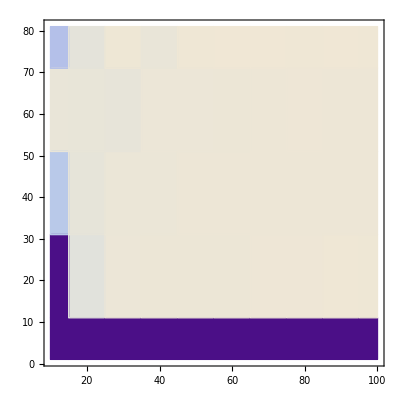

```mathematica
ListDensityPlot[dataPlot,VertexColors->{Red,Green,Yellow,Blue}, Mesh->None,InterpolationOrder->0,PlotRange->All, BoundaryStyle->Red]
```

```mathematica
xy=Table[{i,j},{i,10,100,10},{j,1,100,20}];dataPlot2=Table[Join[Flatten[xy,1][[c]],clusteringData2[[c]]],{c,1,50,1}];
```

```mathematica
ListPlot3D[dataPlot2,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

VertexColors::errlistcol: {RGBColor[1, 0, 0], RGBColor[0, 1, 0], RGBColor[1, 1, 0], RGBColor[0, 0, 1]} must be a list of colors of length 50.

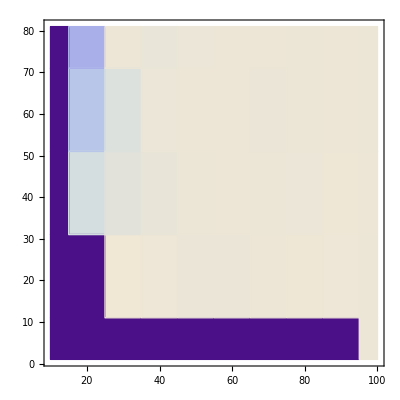

```mathematica
ListDensityPlot[dataPlot2,VertexColors->{Red,Green,Yellow,Blue}, Mesh->None,InterpolationOrder->0,PlotRange->All, BoundaryStyle->Red]
```